# Hydrogen Atom

## Physical Constants

Bohr radius (4 πϵ_0 ℏ^2)/(m e^2) in Å:

```mathematica
a0=UnitConvert[Quantity["Bohr radius"],"Angstroms"]
```

0.529177211 Å

Ground state energy E1 = ℏ^2/(2 m a0^2):

```mathematica
E1=UnitConvert[Quantity["hbar^2/(2 electron mass)"]/a0^2,"eV"]
```

13.6057 eV

## Energy Levels

Define the energy levels in units of E1:

```mathematica
Eval[n_]:=-1/n^2
```

## Radial Potential

Calculate the radial potential in units of E1 with radius in units of a0:

```mathematica
V[r_]:=-2/r
```

Calculate the equivalent 1D potential in units of E1 for u(r) = r R(r) with radius in units of a0:

```mathematica
U[r_,ell_]:=V[r]+ell(ell+1)/r^2
```

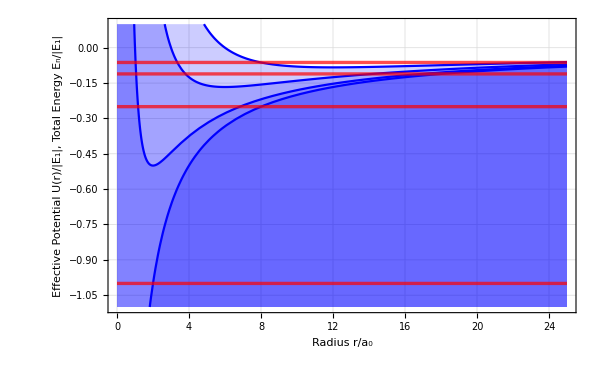

```mathematica
energyPlot=With[{rmax=25},
Plot[{U[r,0],U[r,1],U[r,2],U[r,3]},{r,0,rmax},GridLines->Automatic,Frame->True,FrameLabel->{"Radius r/a_0","Effective Potential U(r)/|E_1|, Total Energy E_n/|E_1|"},LabelStyle->Medium,PlotStyle->Blue,Filling->Bottom,PlotRange->{{0,rmax},{-1.1,0.1}},ImageSize->600,Epilog->{Thickness[0.004],Opacity[0.7],Red,Table[Line[{{0,Eval[n]},{rmax,Eval[n]}}],{n,4}]}
]
]
```

Prepare graphics for Activity 15:

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/Activity15energyPlot.pdf",energyPlot]
```

/Users/david/Documents/uci/Teaching/113A/Activities/Activity15energyPlot.pdf

```mathematica
frame=ListPlot[{},PlotRange->{{0,25},{0,1}},GridLines->Automatic,Frame->True,FrameTicks->{Automatic,None},FrameLabel->{"Radius r/a_0","u(r) = r R_nl(r) [arb.units]"},LabelStyle->Medium,AspectRatio->Full];
```

```mathematica
framePlot=GraphicsGrid[Table[frame,{3},{4}],ImageSize->{1024,768},Spacings->1,AspectRatio->Full];
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/Activity15framePlot.pdf",framePlot]
```

/Users/david/Documents/uci/Teaching/113A/Activities/Activity15framePlot.pdf

## Radial Wavefunction

Define the overall wave function normalization in units of a0^(-3/2):

```mathematica
norm[n_,ell_]:=(2/n^2) Sqrt[(n-ell-1)!/(n+ell)!]
```

Define the normalized radial wave function in units of a0^(-3/2) with r in units of a0:

```mathematica
R[n_,ell_,r_]:=norm[n,ell]Exp[-r/n](2r/n)^ell LaguerreL[n-ell-1,2 ell+1,2r/n]
```

```mathematica
Integrate[r^2 R[3,2,r]^2,{r,0,Infinity}]
```

1

Note that the associated Laguerre polynomial normalization used in Griffiths differs from Mathematica. Compare with Table 4.6 on p.153:

```mathematica
GriffithsL[n_,k_,x_]:=(n+k)! LaguerreL[n,k,x]
```

```mathematica
Expand[GriffithsL[2,1,x]]
```

18-18 x+3 x^2

Compare with Fig.4.4 on p.155:

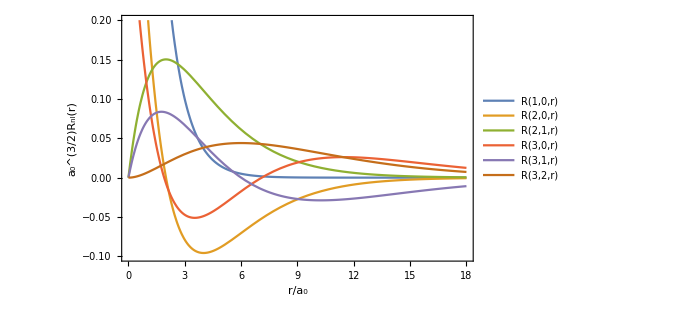

```mathematica
Plot[Tooltip[{
R[1,0,r],
R[2,0,r],R[2,1,r],
R[3,0,r],R[3,1,r],R[3,2,r]
}],{r,0,18},
Frame->True,PlotRange->{-0.1,0.2},PlotLegends->"Expressions",FrameLabel->{"r/a_0","a_0^(3/2)R_nl(r)"},LabelStyle->Medium,ImageSize->500]
```

Plot probability densities r^2 R(r)^2 for ell = 0 states:

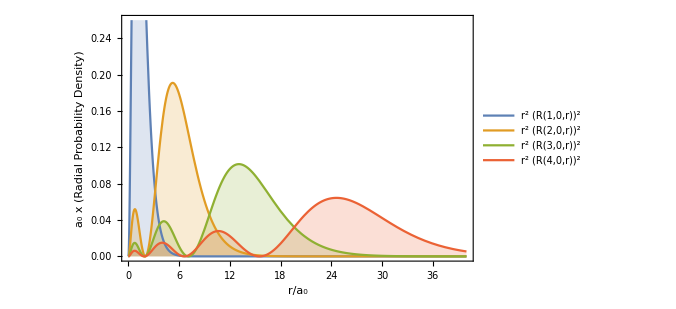

```mathematica
monoPlot=Plot[{
r^2R[1,0,r]^2,
r^2R[2,0,r]^2,
r^2R[3,0,r]^2,
r^2R[4,0,r]^2
},{r,0,40},
Frame->True,PlotRange->{{0,40},{0,0.26}},PlotLegends->Placed["Expressions",Center],FrameLabel->{"r/a_0","a_0 x (Radial Probability Density)"},Filling->0,LabelStyle->Medium,ImageSize->500]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Mini Lectures/monoPlot.pdf",monoPlot]
```

/Users/david/Documents/uci/Teaching/113A/Mini Lectures/monoPlot.pdf

### Lyman-α Transition

```mathematica
lyaPlot=With[{rmax=11},
Show[{
Plot[{U[r,0],U[r,1]},{r,0,rmax},GridLines->Automatic,GridLinesStyle->Directive[Dashed,LightGray],Frame->True,FrameLabel->{"Radius r/a_0","Energy / |E_1|"},LabelStyle->Medium,PlotStyle->Blue,Filling->Bottom,PlotRange->{{0,rmax},{-1.05,0.05}},ImageSize->600,Epilog->{Thickness[0.004],Opacity[0.7],Red,Table[Line[{{0,Eval[n]},{rmax,Eval[n]}}],{n,2}]}
],
Plot[{
Eval[1]+r^2 R[1,0,r]^2,
Eval[2]+r^2 R[2,0,r]^2,
Eval[2]+r^2 R[2,1,r]^2
},{r,0,rmax},Filling->{1->Eval[1],2->Eval[2],3->Eval[2]},PlotStyle->Directive[Thin,Gray],FillingStyle->Directive[Gray,Opacity[0.2]]]
},
ImageMargins->4
]
]
```

-Graphics-

```mathematica
Export["/Users/david/Desktop/LyaQM.pdf",lyaPlot]
```

/Users/david/Desktop/LyaQM.pdf

## 3D Wavefunction

Define the wave function in units of a0^(-3/2) using polar coordinates with r in units of a0:

```mathematica
ψ[n_,ell_,m_,r_,θ_,ϕ_]:=R[n,ell,r]SphericalHarmonicY[ell,m,θ,ϕ]
```

Define the wave function in Cartesian coordinates:

```mathematica
ψxyz[n_,ell_,m_,x_,y_,z_]:=R[n,ell,Sqrt[x^2+y^2+z^2]]SphericalHarmonicY[ell,m,ArcTan[z,Sqrt[x^2+y^2]],ArcTan[x,y]]
```

```mathematica
laplacian[n_,ell_,m_,x_,y_,z_]:=Laplacian[ψxyz[n,ell,m,xx,yy,zz],{xx,yy,zz}]/.{xx->x,yy->y,zz->z}
```

## Visualization

### 2D Plots

Tabulate 2D function values in the upper-right quadrant:

```mathematica
tabulate2D[f_,range_,npts_]:=
With[{
grid=(Range[npts]-0.5)range/npts
},
Table[f[x1,x2],{x2,grid},{x1,grid}]
]
```

Assemble the four quadrants of a symmetric function using only calculations in the upper-right quadrant:

```mathematica
tabulate2Dsymm[f_,range_,npts_]:=
Module[{UR,UL,LL,LR},
UR=tabulate2D[f,range,npts];
UL=Reverse[UR,2];
LL=Reverse[UL,1];
LR=Reverse[UR,1];
ArrayFlatten[{{LL,LR},{UL,UR}}]
]
```

Define a color function that emphasizes structure in the tails:

```mathematica
tailColorMap[z_]:=ColorData["SunsetColors"][z^0.25]
```

### Probability Densities in the (x,z) plane

Make (x,z) probability density plots using a non-linear color map that emphasizes the nodal structure:

```mathematica
Clear[xzPlot]
xzPlot[n_,ell_,m_,OptionsPattern[]]:=
With[{
max=OptionValue["max"],
npts=OptionValue["npts"],
gopts=OptionValue["gopts"],
label=OptionValue["label"],
labelSize=OptionValue["labelSize"],
defaults={
PlotRange->All,PlotRangePadding->None,Frame->False,FrameTicks->None,ColorFunction->tailColorMap
}
},
Module[{pdf,data},
pdf=Function[{x,z},Evaluate[Simplify[Abs[ψxyz[n,ell,m,x,0,z]]^2]]];
data=tabulate2Dsymm[pdf,max,npts];
Rasterize[
ListDensityPlot[
data,gopts,defaults,
Epilog->If[label===True,{
Text[Style[Superscript["|"<>ToString[n]<>","<>ToString[ell]<>","<>ToString[m]<>"|",2],FontColor->White,FontSize->labelSize,FontFamily->"Times",FontWeight->"Bold"],Scaled[{0.5,0.02}],{0,-1}]
},{}]
]
]
]
]
Options[xzPlot]={"max"->20,"npts"->100,"gopts"->{},"label"->False,"labelSize"->36};
```

Reproduce this wikipedia plot http://en.wikipedia.org/wiki/Hydrogen_atom#/media/File:HAtomOrbitals.png:

```mathematica
With[{
opts={"max"->20}
},
Rasterize[
GraphicsGrid[{
{
xzPlot[1,0,0,opts]
},
{
xzPlot[2,0,0,opts],
xzPlot[2,1,0,opts]
},
{
xzPlot[3,0,0,opts],
xzPlot[3,1,0,opts],
xzPlot[3,2,0,opts]
}
},
ImageSize->500,Spacings->0
]
]
]
```

-Graphics-

Make a plot for Activity 15:

```mathematica
randomNodesPlot=With[{
opts={"max"->30}
},
Rasterize[
GraphicsGrid[{
{
xzPlot[5,1,0,opts],
xzPlot[3,0,0,opts],
xzPlot[3,2,0,opts],
xzPlot[5,4,0,opts]
},
{
xzPlot[4,3,0,opts],
xzPlot[5,2,0,opts],
xzPlot[4,0,0,opts],
xzPlot[4,2,0,opts]
},
{
xzPlot[5,0,0,opts],
xzPlot[3,1,0,opts],
xzPlot[5,3,0,opts],
xzPlot[4,1,0,opts]
}
},
ImageSize->{1024,768},Spacings->1
]
]
]
```

-Graphics-

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/repo/web/img/randomNodes.png",randomNodesPlot]
```

/Users/david/Documents/uci/Teaching/113A/repo/web/img/randomNodes.png

Make a plot for Mini Lecture 14:

```mathematica
hydrogen123Plot=With[{
opts={
"max"->25,
"label"->True
},
none=Graphics[]
},
Rasterize[
GraphicsGrid[{
{
xzPlot[2,0,0,opts],xzPlot[2,1,0,opts],xzPlot[3,0,0,opts],xzPlot[3,1,0,opts],xzPlot[3,2,0,opts]
},
{
none,xzPlot[2,1,1,opts],none,xzPlot[3,1,1,opts],xzPlot[3,2,1,opts]
},
{
xzPlot[1,0,0,opts],none,none,none,xzPlot[3,2,2,opts]
}
},
ImageSize->1024,Spacings->1
]
]
]
```

-Graphics-

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/repo/web/img/hydrogen123.png",hydrogen123Plot]
```

/Users/david/Documents/uci/Teaching/113A/repo/web/img/hydrogen123.png

```mathematica
hydrogen4Plot=With[{
opts={
"max"->31.25, (* same pixel scale as 123 plot *)
"label"->True
},
none=Graphics[]
},
Rasterize[
GraphicsGrid[{
{
xzPlot[4,0,0,opts],xzPlot[4,1,0,opts],xzPlot[4,2,0,opts],xzPlot[4,3,0,opts]
},
{
none,xzPlot[4,1,1,opts],xzPlot[4,2,1,opts],xzPlot[4,3,1,opts]
},
{
none,none,xzPlot[4,2,2,opts],xzPlot[4,3,2,opts]
},
{
none,none,none,xzPlot[4,3,3,opts]
}
},
ImageSize->1024,Spacings->1
]
]
]
```

-Graphics-

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/repo/web/img/hydrogen4.png",hydrogen4Plot]
```

/Users/david/Documents/uci/Teaching/113A/repo/web/img/hydrogen4.png

### Azimuthal functions in the (x,y) plane

```mathematica
Clear[xyPlot]
xyPlot[n_,m_,t_,OptionsPattern[]]:=
With[{
labelSize=OptionValue["labelSize"]
},
Show[{
DensityPlot[Cos[(m ArcTan[x,y]-t/n^2)],{x,-1,+1},{y,-1,+1},
PlotRangePadding->None,Frame->False,FrameTicks->None,PlotPoints->100,
ColorFunction->(ColorData["TemperatureMap"][(#+1)/2]&),ColorFunctionScaling->False,
Epilog->{
Text[Style["Re(n="<>ToString[n]<>",m="<>ToString[m]<>")",FontColor->Black,FontSize->labelSize,FontFamily->"Times",FontWeight->"Bold"],Scaled[{0.02,0.01}],{-1,-1}]
}
],
PolarPlot[{0.8,0.8+0.1 Cos[(m ϕ-t/n^2)],0.8+0.1 Sin[(m ϕ-t/n^2)]},{ϕ,0,2π},
PlotStyle->{{White},{Black},{Black,Dashed}}]
}]
]
Options[xyPlot]={"labelSize"->Scaled[0.06]};
```

```mathematica
xyFrame[t_]:=
With[{none=Graphics[]},
Module[{P},
P[n_,m_]:=xyPlot[n,m,t];
Rasterize[
GraphicsGrid[{
{P[6,-1],P[6,-2],P[6,-3],P[6,-4],P[6,-5]},
{P[3,-1],P[3,-2],none,none,none},
{P[3,+1],P[3,+2],none,none,none},
{P[6,+1],P[6,+2],P[6,+3],P[6,+4],P[6,+5]}
},
ImageSize->{1024,768},Spacings->{16,1}
]
]
]
]
```

```mathematica
azimuthalFramePlot=xyFrame[36 2π]
```

-Graphics-

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/azimuthalFrame.png",azimuthalFramePlot]
```

/Users/david/Documents/uci/Teaching/113A/Activities/azimuthalFrame.png

```mathematica
Timing[
frames=With[{nframes=300},
Module[{tvec},
tvec=36 2π Range[0,nframes-1]/nframes ;
Table[xyFrame[t],{t,tvec}]
]
];
]
```

{2222.17,Null}

```mathematica
Timing[
Export["/Users/david/Documents/uci/Teaching/113A/repo/web/img/azimuthal.mov",
frames,"FrameRate"->30,AnimationRepetitions->Infinity
];
]
```

{20.945,Null}

### 2D Contour Plots of ψ and ∇^2 ψ.

Plot the density of a real-valued function in the (x/a0,z/a0).  Increase the AntiAliasing Quality slider under Preferences to get smooth contour lines:

```mathematica
Needs["DeepZot`PlotTools`"]
```

```mathematica
density[f_,OptionsPattern[]]:=
With[{
max=OptionValue["max"],
zmax=OptionValue["zmax"],
gopts=OptionValue["gopts"],
nlevels=OptionValue["nlevels"],
defaults={
PlotPoints->20,ColorFunctionScaling->None,ClippingStyle->{Blue,Red},FrameLabel->{"x/a_0","z/a_0"},LabelStyle->Medium,PlotRangePadding->None,GridLines->Automatic,GridLinesStyle->Directive[Black,Opacity[0.2]],Method->{"GridLinesInFront"->True}
}
},
Module[{levels,styles},
levels=(zmax/nlevels) Range[-nlevels,+nlevels];
styles=ConstantArray[Directive[Opacity[0.3],Thickness[0.004],Black],2 nlevels+1];
styles[[1]]=styles[[1+nlevels]]=styles[[-1]]=Directive[Thickness[0.004],Black];
Show[{
DensityPlot[f[x,z],{x,0,+max},{z,0,+max},gopts,defaults,ColorFunction->(temperatureMap[(#+zmax)/(2 zmax)]&),PlotRange->{-zmax,+zmax}],
ContourPlot[f[x,z],{x,0,+max},{z,0,+max},Contours->levels,ContourStyle->styles,ContourShading->None,ContourStyle->Thickness[0.004]]
}]
]
]
Options[density]={"max"->12,"zmax"->0.1,"nlevels"->10,"gopts"->{}};
```

Make a separate colorbar legend (for some reason, PlotLegends->... gives an error):

```mathematica
legend[zmax_]:=BarLegend[{(temperatureMap[(#+zmax)/(2 zmax)]&),{-zmax,+zmax}},LabelStyle->Directive[Medium]]
```

Draw some examples for activity 15 (these take a while):

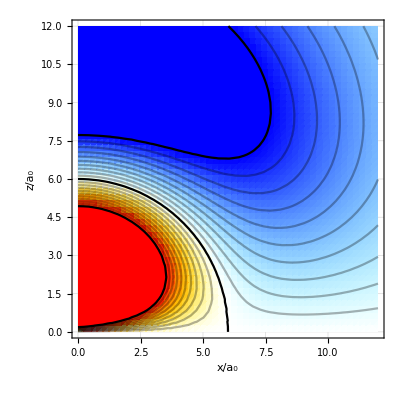

```mathematica
R1C1=density[ψxyz[3,1,0,#1,0,#2]&,gopts->{PlotPoints->50},zmax->0.01]
```

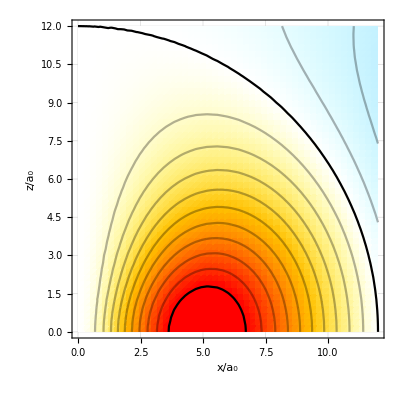

```mathematica
R1C2=density[ψxyz[4,2,-2,#1,0,#2]&,gopts->{PlotPoints->50},zmax->0.01]
```

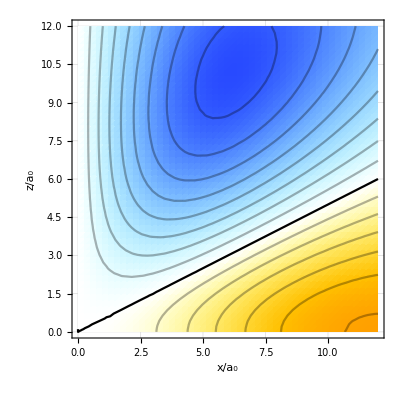

```mathematica
R1C3=density[ψxyz[4,3,1,#1,0,#2]&,gopts->{PlotPoints->50},zmax->0.01]
```

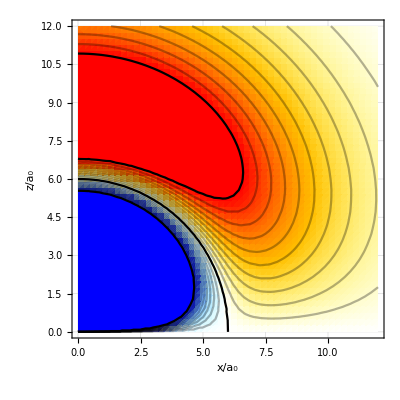

```mathematica
R2C1=density[laplacian[3,1,0,#1,0,#2]&,gopts->{PlotPoints->50},zmax->0.001]
```

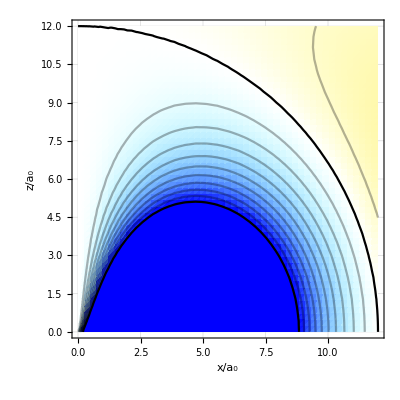

```mathematica
R2C2=density[laplacian[4,2,-2,#1,0,#2]&,gopts->{PlotPoints->50},zmax->0.001]
```

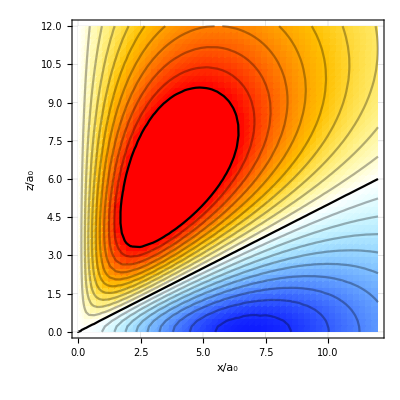

```mathematica
R2C3=density[laplacian[4,3,1,#1,0,#2]&,gopts->{PlotPoints->50},zmax->0.001]
```

```mathematica
wfGrid=Rasterize[GraphicsGrid[{
{R1C1,R1C2,R1C3},
{R2C1,R2C2,R2C3}
},ImageSize->1000,Spacings->1
]]
```

-Graphics-

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/Activity15wfGrid.png",wfGrid]
```

/Users/david/Documents/uci/Teaching/113A/Activities/Activity15wfGrid.png

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/Activity15legend1.pdf",legend[0.01]]
```

/Users/david/Documents/uci/Teaching/113A/Activities/Activity15legend1.pdf

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/Activity15legend2.pdf",legend[0.001]]
```

/Users/david/Documents/uci/Teaching/113A/Activities/Activity15legend2.pdf

Work out an explicit example of calculating the energy-level difference between two stationary states:

```mathematica
DEcalc[n1_,ell1_,m1_,n2_,ell2_,m2_,x_,y_,z_]:=
Module[{N1,D1,N2,D2},
N1=laplacian[n1,ell1,m1,x,y,z]//N;
D1=ψxyz[n1,ell1,m1,x,y,z]//N;
N2=laplacian[n2,ell2,m2,x,y,z]//N;
D2=ψxyz[n2,ell2,m2,x,y,z]//N;
Print["ψ_1 has n=",n1,",ell=",ell1,",m=",m1];
Print["ψ_2 has n=",n2,",ell=",ell2,",m=",m2];
Print["Using r/a_0 =(",x,",",y,",",z,") where:"];
Print["a_0^(7/2)∇^2 ψ_1(r) = ",N1," and a_0^(3/2)ψ_1(r)= ",D1," with a ratio a_0^2∇^2 ψ_1(r)/ψ_1(r) = (E_n1-V(r))/E_1 = ",N1/D1];
Print["a_0^(7/2)∇^2 ψ_2(r) = ",N2," and a_0^(3/2)ψ_2(r)= ",D2," with a ratio a_0^2∇^2 ψ_2(r)/ψ_2(r) = (E_n2-V(r))/E_1 = ",N2/D2];
Print["ΔE = ",N1/D1-N2/D2,", n_1^-2 - n_2^-2 = ",n1^-2 - n2^-2," = ",N[n1^-2 - n2^-2]];
]
```

Use a large value of r so that the relative contributions of V(r) are smaller and there is less round-off error when calculating the energy difference:

```mathematica
DEcalc[3,1,0,4,2,-2,10,0,10]
```

ψ_1 has n=3,ell=1,m=0

ψ_2 has n=4,ell=2,m=-2

Using r/a_0 =(10,0,10) where:

a_0^(7/2)∇^2 ψ_1(r) = 0.000218021 and a_0^(3/2)ψ_1(r)= -0.00719299 with a ratio a_0^2∇^2 ψ_1(r)/ψ_1(r) = (E_n1-V(r))/E_1 = -0.0303102

a_0^(7/2)∇^2 ψ_2(r) = 0.000110823 and a_0^(3/2)ψ_2(r)= -0.00140421 with a ratio a_0^2∇^2 ψ_2(r)/ψ_2(r) = (E_n2-V(r))/E_1 = -0.0789214

ΔE = 0.0486111, n_1^-2 - n_2^-2 = 7/144 = 0.0486111

```mathematica
DEcalc[3,1,0,4,3,1,10,0,10]
```

ψ_1 has n=3,ell=1,m=0

ψ_2 has n=4,ell=3,m=1

Using r/a_0 =(10,0,10) where:

a_0^(7/2)∇^2 ψ_1(r) = 0.000218021 and a_0^(3/2)ψ_1(r)= -0.00719299 with a ratio a_0^2∇^2 ψ_1(r)/ψ_1(r) = (E_n1-V(r))/E_1 = -0.0303102

a_0^(7/2)∇^2 ψ_2(r) = 0.000490798 and a_0^(3/2)ψ_2(r)= -0.00621882 with a ratio a_0^2∇^2 ψ_2(r)/ψ_2(r) = (E_n2-V(r))/E_1 = -0.0789214

ΔE = 0.0486111, n_1^-2 - n_2^-2 = 7/144 = 0.0486111

```mathematica
DEcalc[4,2,-2,4,3,1,10,0,10]
```

ψ_1 has n=4,ell=2,m=-2

ψ_2 has n=4,ell=3,m=1

Using r/a_0 =(10,0,10) where:

a_0^(7/2)∇^2 ψ_1(r) = 0.000110823 and a_0^(3/2)ψ_1(r)= -0.00140421 with a ratio a_0^2∇^2 ψ_1(r)/ψ_1(r) = (E_n1-V(r))/E_1 = -0.0789214

a_0^(7/2)∇^2 ψ_2(r) = 0.000490798 and a_0^(3/2)ψ_2(r)= -0.00621882 with a ratio a_0^2∇^2 ψ_2(r)/ψ_2(r) = (E_n2-V(r))/E_1 = -0.0789214

ΔE = 1.38778×10^-17, n_1^-2 - n_2^-2 = 0 = 0.

```mathematica
Table[n1^-2 - n2^-2,{n1,4},{n2,4}]//TableForm
```

0 | 3/4 | 8/9 | 15/16
-3/4 | 0 | 5/36 | 3/16
-8/9 | -5/36 | 0 | 7/144
-15/16 | -3/16 | -7/144 | 0

```mathematica
Table[N[n1^-2 - n2^-2],{n1,4},{n2,4}]//TableForm
```

0. | 0.75 | 0.888889 | 0.9375
-0.75 | 0. | 0.138889 | 0.1875
-0.888889 | -0.138889 | 0. | 0.0486111
-0.9375 | -0.1875 | -0.0486111 | 0.